# ΔE vs (Ei-ESQPT)

```mathematica
Clear[γx];
j=1000;
```

```mathematica
γx=-(2j-1)/((2j-1698)Sqrt[3] );
c[j_,γx_,γy_]:= 1/(2(2j-1))(γx+γy);
γm=Sign[γx]Min[Abs[γx],Abs[3γx]];
ESQPT=N[ (γm +γm^-1 )/2+c[j,γx,3γx],16];
```

```mathematica
ESQPT
```

-2.045458745629409

## Datos 100

```mathematica
Datos100 = Import["/home/chay/Descargas/AvancesT/12_J/Espectros/100/EnergyAC100.dat"];
```

```mathematica
Lista100 =Flatten[Datos100]/100;
```

```mathematica
region100 = Lista100[[61;;76]]
```

{-2.05642,-2.05184,-1.99994,-1.99971,-1.93627,-1.93627,-1.86608,-1.86608,-1.79037,-1.79037,-1.70977,-1.70977,-1.62469,-1.62469,-1.53541,-1.53541}

```mathematica
dif100 = Table[region100[[2*i]]-region100[[2*i-1]],{i,1,8}];
prom100 =Table[(region100[[2*i]]+region100[[2*i-1]])*0.5-ESQPT,{i,1,8}];
```

```mathematica
data100 = Transpose[{prom100,dif100}]
```

{{0.0297955,0.00457352},{0.0840987,0.000232109},{0.147656,5.72855×10^-6},{0.217844,8.87197×10^-8},{0.293552,9.25719×10^-10},{0.374153,6.70108×10^-12},{0.459236,3.39728×10^-14},{0.548511,0.}}

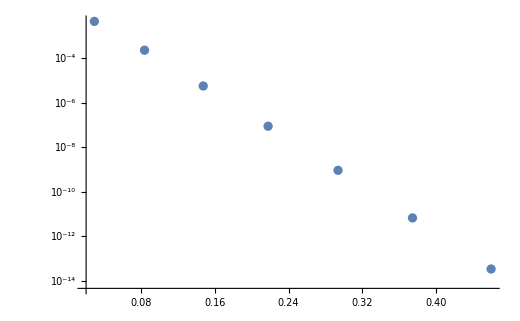

```mathematica
ListLogPlot[data100,PlotRange->Full]
```

## Datos 200

```mathematica
Datos200 = Import["/home/chay/Descargas/AvancesT/12_J/Espectros/200/EnergyAC200.dat"];
```

```mathematica
Lista200 =Flatten[Datos200]/200;
```

```mathematica
region200 = Lista200[[120;;135]]
```

{-2.0658,-2.06112,-2.04151,-2.04099,-2.015,-2.01497,-1.98596,-1.98596,-1.95482,-1.95482,-1.92187,-1.92187,-1.88733,-1.88733,-1.85133,-1.85133}

```mathematica
dif200 = Table[region200[[2*i]]-region200[[2*i-1]],{i,1,8}];
prom200 =Table[(region200[[2*i]]+region200[[2*i-1]])*0.5-ESQPT,{i,1,8}];
```

```mathematica
data200 = Transpose[{prom200,dif200}]
```

{{0.0057049,0.00467853},{0.0279136,0.000513249},{0.054181,0.000025216},{0.0832026,8.40459×10^-7},{0.114346,2.10422×10^-8},{0.147289,4.13488×10^-10},{0.181831,6.53899×10^-12},{0.217831,8.43769×10^-14}}

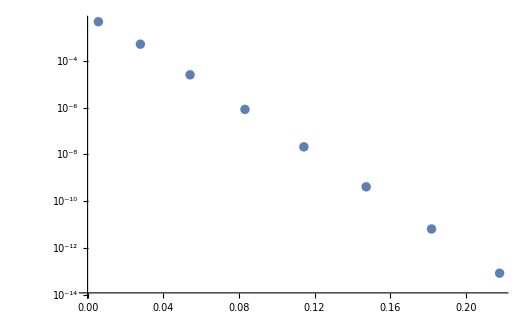

```mathematica
ListLogPlot[data200]
```

## Datos 500

```mathematica
Datos500 = Import["/home/chay/Descargas/AvancesT/12_J/Espectros/500/EnergyAC500.dat"];
```

```mathematica
Lista500 =Flatten[Datos500]/500;
```

```mathematica
region500 = Lista500[[299;;314]];
```

```mathematica
dif500 = Table[region500[[2*i]]-region500[[2*i-1]],{i,1,8}];
prom500 =Table[(region500[[2*i]]+region500[[2*i-1]])*0.5-ESQPT,{i,1,8}];
```

```mathematica
data500 = Transpose[{prom500,dif500}]
```

{{0.000881582,0.00214793},{0.00847543,0.000380177},{0.0172716,0.0000313642},{0.0269264,1.87931×10^-6},{0.0372002,9.14842×10^-8},{0.0479794,3.7747×10^-9},{0.0591956,1.35192×10^-10},{0.0708017,4.26903×10^-12}}

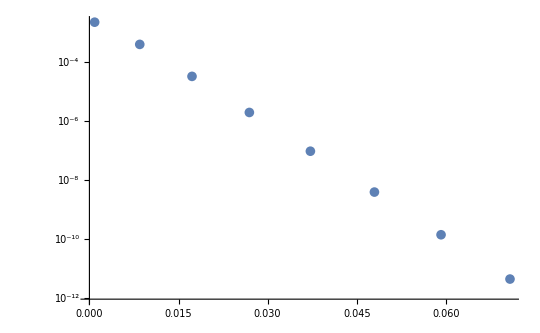

```mathematica
ListLogPlot[data500]
```

## Datos 800

```mathematica
Datos800 = Import["/home/chay/Descargas/AvancesT/12_J/Espectros/800/EnergyAC800.dat"];
```

```mathematica
Lista800 =Flatten[Datos800]/800;
```

```mathematica
region800 = Lista800[[479;;494]];
```

```mathematica
dif800 = Table[region800[[2*i]]-region800[[2*i-1]],{i,1,8}];
prom800 =Table[(region800[[2*i]]+region800[[2*i-1]])*0.5-ESQPT,{i,1,8}];
```

```mathematica
data800 = Transpose[{prom800,dif800}]
```

{{0.00220127,0.000766809},{0.00688184,0.000106889},{0.0121663,9.16436×10^-6},{0.0178465,6.26386×10^-7},{0.0238257,3.64797×10^-8},{0.0300531,1.86566×10^-9},{0.0364963,8.53224×10^-11},{0.0431325,3.53273×10^-12}}

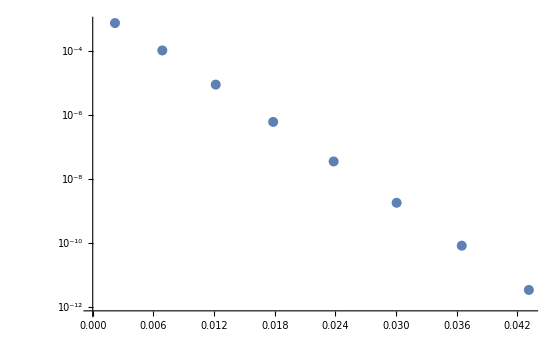

```mathematica
ListLogPlot[data800]
```

## Datos 1000

```mathematica
Datos1000 = Import["/home/chay/Descargas/AvancesT/12_J/Espectros/1000/EnergyAC1000.dat"];
```

```mathematica
Lista1000 =Flatten[Datos1000]/1000;
```

```mathematica
region1000 = Lista1000[[599;;614]];
```

```mathematica
dif1000 = Table[region1000[[2*i]]-region1000[[2*i-1]],{i,1,8}];
prom1000 =Table[(region1000[[2*i]]+region1000[[2*i-1]])*0.5-ESQPT,{i,1,8}];
```

```mathematica
data1000 = Transpose[{prom1000,dif1000}]
```

{{0.0024525,0.000436352},{0.00620564,0.000056123},{0.0103767,4.93411×10^-6},{0.014824,3.57324×10^-7},{0.0194842,2.246×10^-8},{0.0243227,1.25708×10^-9},{0.0293168,6.36491×10^-11},{0.0344503,2.94786×10^-12}}

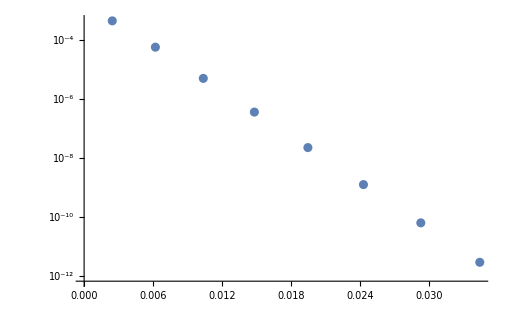

```mathematica
ListLogPlot[data1000]
```

```mathematica
datos = {data100,data200,data500,data800,data1000};
out = "/home/chay/Descargas/AvancesT/12_J/Espectros/DeltaEi.dat";
```

```mathematica
Export[out, N[datos,16]]
```

/home/chay/Descargas/AvancesT/12_J/Espectros/DeltaEi.dat